BJK - 22/06/2017

## Parameters

Number of protons and neutrons in Xe, Ar and Si

```mathematica
NpXe = 54;
NnXe = 77;
NpAr = 18;
NnAr = 22; 
NpSi = 14;
NnSi = 14;
```

## Calculations

Take two nuclear targets:

```mathematica
A = {{Np1,Nn1},{Np2,Nn2}};
```

For two targets, we can obtain four exact solutions for the Majorana couplings. Calculate these four solutions to Eq. B1 and B2 (up to some normalisation):

```mathematica
ClearAll[σ1, σ2]
```

```mathematica
{λpMa, λnMa} =  Inverse[A].{Sqrt[σ1] ,Sqrt[σ2]}
{λpMb, λnMb} =  Inverse[A].{Sqrt[σ1] ,-Sqrt[σ2]}
{λpMc, λnMc} =  Inverse[A].{-Sqrt[σ1] ,-Sqrt[σ2]}
{λpMd, λnMd} =  Inverse[A].{-Sqrt[σ1] ,Sqrt[σ2]}
```

{(Nn2 √σ1)/(Nn2 Np1-Nn1 Np2)-(Nn1 √σ2)/(Nn2 Np1-Nn1 Np2),-(Np2 √σ1)/(Nn2 Np1-Nn1 Np2)+(Np1 √σ2)/(Nn2 Np1-Nn1 Np2)}

{(Nn2 √σ1)/(Nn2 Np1-Nn1 Np2)+(Nn1 √σ2)/(Nn2 Np1-Nn1 Np2),-(Np2 √σ1)/(Nn2 Np1-Nn1 Np2)-(Np1 √σ2)/(Nn2 Np1-Nn1 Np2)}

{-(Nn2 √σ1)/(Nn2 Np1-Nn1 Np2)+(Nn1 √σ2)/(Nn2 Np1-Nn1 Np2),(Np2 √σ1)/(Nn2 Np1-Nn1 Np2)-(Np1 √σ2)/(Nn2 Np1-Nn1 Np2)}

{-(Nn2 √σ1)/(Nn2 Np1-Nn1 Np2)-(Nn1 √σ2)/(Nn2 Np1-Nn1 Np2),(Np2 √σ1)/(Nn2 Np1-Nn1 Np2)+(Np1 √σ2)/(Nn2 Np1-Nn1 Np2)}

Calculate Majorana cross section for a 3rd target, using these values:

```mathematica
σ3a = (λpMa Np3 + λnMa Nn3)^2;
σ3b = (λpMb Np3 + λnMb Nn3)^2;
σ3c = (λpMc Np3 + λnMc Nn3)^2;
σ3d = (λpMd Np3 + λnMd Nn3)^2;
```

Calculate discrepancy between Majorana and Dirac cross section for Xe:

```mathematica
Clear[GetDeviationXe]
GetDeviationXe[cp_, cn_, f_]:=
(
Block[{σ1 = (cp NpSi + cn NnSi)^2 + 2 cp cn (f-1) NpSi NnSi,
	σ2 = (cp NpAr + cn NnAr)^2 + 2 cp cn (f-1) NpAr NnAr,
	σ3 = (cp NpXe + cn NnXe)^2 + 2 cp cn (f-1) NpXe NnXe,
	Np1 = NpSi, Nn1 = NnSi, 
	Np2 = NpAr, Nn2 = NnAr,
	Np3 = NpXe, Nn3 = NnXe},

Return[  Min[{((σ3a - σ3)^2/σ3^2),
((σ3b - σ3)^2/σ3^2),
((σ3c - σ3)^2/σ3^2),
((σ3d - σ3)^2/σ3^2)}]]

(*Return[((σ3a - σ3)/σ3)^2]*)
])
```

Calculate over a grid of values and output to file:

```mathematica
AnalyticVals = Flatten[Table[{f, rnp, GetDeviationXe[1.0, rnp, f]}, {f, -1.0, -0.94,0.001}, {rnp, 0.5, 1.1, 0.01}], 1];
```

```mathematica
Export[NotebookDirectory[]<>"../results/AnalyticEstimate.dat", AnalyticVals]
```

/Users/bradkav/Code/AntiparticleDM/calc/../results/AnalyticEstimate.dat

Plot for illustration:

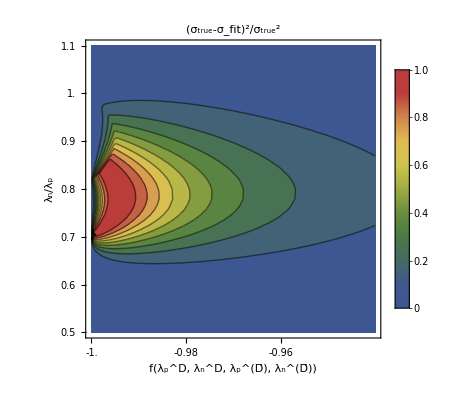

```mathematica
pEstimate = ContourPlot[ GetDeviationXe[1.0, rnp, f],{f, -1.0,-0.94 }, {rnp, 0.5,1.1} , PlotRange->All, Exclusions->None,ColorFunction->"DarkRainbow",PlotLegends->BarLegend[{"DarkRainbow",{0, 1}}],FrameLabel->{"f(λ_p^D, λ_n^D, λ_p^(D̄), λ_n^(D̄))", "λ_n/λ_p"},BaseStyle->{FontSize->18, FontFamily->"Times", FontColor->Black},  ImageSize->400, ImageMargins->5, AspectRatio->1,
ColorFunctionScaling->True,AxesStyle->Directive[Black,Thickness[0.003]], PlotLabel->"(σ_true-σ_fit)^2/σ_true^2", PlotRange->{{-1,-0.94},{0.5,1.1}}, 
Frame->True,FrameTicks->{{{0.5,0.6,0.7,0.8,0.9,1.0,1.1},None},{{-1.00, -0.98, -0.96},None}}]
```